# SRBench Competition Abstract

StackGP was used to generate the models in this submission. I used the Python based StackGP system, which is available in the StackGP.py file in the submission. For each problem I began by running a standard model search using default settings of StackGP with all of the variables in the data sets. From there I analyzed the populations to see which variables stood out as important. I then analyzed all of the input variables by doing a cross-correlation analysis, as well as a cross-modelling analysis. This revealed some relationships between some of the variables, so that some variables could be removed. These analyses are stored in the Mathematica notebooks “model1.nb”, “model2.nb”, and “model3.nb”. From there I ran some runs with StackGP using active learning to train models using the most informative points, selected iteratively. Each of the steps are described in more detail below. Note that in the figures developed in Mathematica, since indexing begins at 1, there is an offset from the true input labels (example: x1 in Mathematica figure = x0 in original data).

## Dataset 1

Initially, I plotted each of the input variables against the response to see if any obvious trends arise. The results are here, and don’t seem to show any obvious trends.

We do see though that most of the input variables are sampled from a bimodal distribution, while the response is a normal distribution.

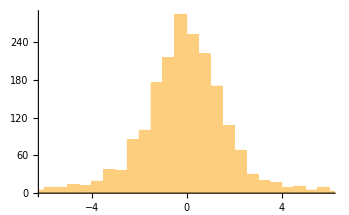
```mathematica
-Graphics--Graphics-
```

An initial run showed that 3 of the variables dominated. These correspond to variables x0, x1, and x6 from the initial set. We narrow the focus to these variables in the final model development.

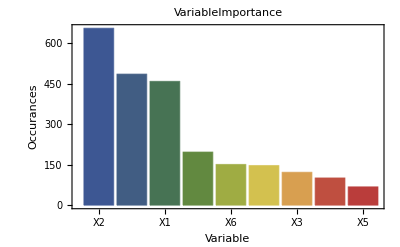

From the cross-modelling analysis we see that variable 3 appears to be highly correlated to variable 0, likely indicating it is a noisy version of variable 0. Variable 2 was found to have a high correlation to x0+x1, indicating that either x0 and x1 are noisy versions of x2, or x2 is composed of x0 and x1. Since x1 and x0 appeared more frequently in the search, it is assumed that those are informative and x2 is a noisy version of x0+x1. Variable 4 was found to have a high correlation to variable 1, which likely indicates it is a noisy version of 1. Variable 5 was found to have a high correlation to the equation 1/(π+x6)-x2. Variable 6 did not appear to have strong relationships with any other variables. Variable 7 had a high correlation with variable 0. Variable 8 appeared to be strongly correlated to x1.